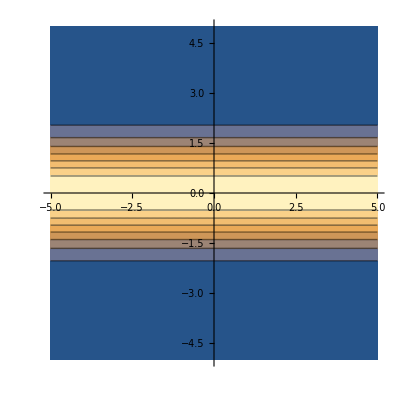

```mathematica
f[x1_,x2_]:=1/(√(2 π σ^2))Exp[-x2^2/(2 σ^2)]
σ=1;
Show[Plot[0,{x,-5,5},PlotRange->{{-5,5},{-5,5}},AspectRatio->1],ContourPlot[f[x,y],{x,-5,5},{y,-5,5},PlotPoints->50]]
```

```mathematica
ϕ[x1_,x2_]:=({{Cos[a], -Sin[a]}, {Sin[a], Cos[a]}}).({{x1}, {x2}}) + ({{μx}, {μy}}) (*= ({{ϕ1[x1,x2]}, {ϕ2[x1,x2]}})=({{y1}, {y2}})  *)
```

```mathematica
Clear[a,σ,μx,μy]
ϕ[x,y]//MatrixForm
```

```mathematica
({{μx+x Cos[a]-y Sin[a]}, {μy+y Cos[a]+x Sin[a]}})
```

```mathematica
(* g[y1,y2]= f[ϕ1^-1[y1,y2],ϕ2^-1[y1,y2]]*DetJ[ϕ^-1]  *)
solution = Solve[{y1==Evaluate[ϕ[x,y][[1,1]]],y2==Evaluate[ϕ[x,y][[2,1]]]},{x,y}]//FullSimplify
```

{{x→(y1-μx) Cos[a]+(y2-μy) Sin[a],y→(y2-μy) Cos[a]+(-y1+μx) Sin[a]}}

```mathematica
f[x/.solution[[1,1]],y/.solution[[1,2]]]
```

(ⅇ^(-((y2-μy) Cos[a]+(-y1+μx) Sin[a])^2/(2 σ^2)))/(√(2 π) √(σ^2))

```mathematica
g[x_,y_]:=1/(√(2 π σ^2))Exp[(-((y-μy)*Cos[a]-(x-μx)*Sin[a])^2)/(2 σ^2)]
```

(ⅇ^(-1/2 ((1-x)/2+1/2 √3 (3+y))^2))/(√(2 π))

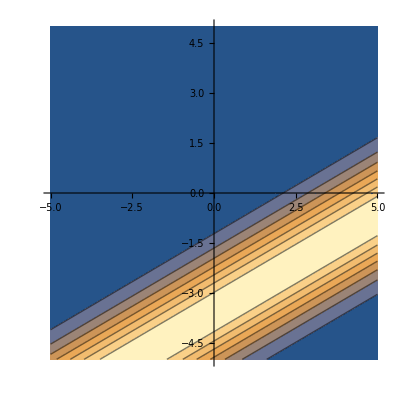

```mathematica
a=π/6;
μx=1;
μy=-3;
σ=1;
g[x,y]
Show[Plot[0,{x,-5,5},PlotRange->{{-5,5},{-5,5}},AspectRatio->1],ContourPlot[g[x,y],{x,-5,5},{y,-5,5},PlotPoints->50]]
```